```mathematica
(* n=0.70 limit derivation *)
lCoeff=((2 n+1)/n)^n;
eta1 = ((2 lCoeff^(3/n-1)  R)/((2 n+1) (3 n+2))-(lCoeff^(1/n)  cott)/(2 n+1));
eta3 =-R^3 ((8 lCoeff^((7/n)-3) (408 n^5+3414 n^4+8935 n^3+9890 n^2+4905 n +900))/((2n+1)^3 (3n+2)^2(4n+3)(5n+4)(6n+5)(7n+6))) +R^2 cott ((3 lCoeff^(5/n-2) (244 n^5+2248 n^4+5675 n^3+5940 n^2+2776 n+480))/((2n+1)^3 (3n+2)^2 (4n+3) (5n+4)(6n+5)))-R cott^2 ((2 lCoeff^(3/n-1))/((2n+1)^2(3n+2)))+cott ((lCoeff^(1/n) (2n+7))/(3(2n-1)(4n+1)))-R ((lCoeff^(3/n-1) (988 n^6+5666 n^5+11622 n^4+10825 n^3+5008 n^2+1120n+96))/((2n-1)(2n+1)^2 (3n+1)(3n+2)(4n+1)(5n+2)(5n+3)));
```

```mathematica
eta1N1Mod=eta1/.{n->13/25}//Simplify
eta3N1Mod=eta3/.{n->13/25, R->((3n+2)/2 ((2n+1)/n)^(n-2) cott)}//Simplify
```

-(25 cott)/13+(63750 (51/13)^(12/25) R)/15041

(85425 cott)/1001-(4045198955775 (51/13)^(12/25) cott (2+1/n)^(-2+n) (2+3 n))/13638456832-(15625 (51/13)^(12/25) cott^3 (2+1/n)^(-2+n) (2+3 n))/15041+(137368423646875 (51/13)^(24/25) cott^3 (2+1/n)^(2 (-2+n)) (2+3 n)^2)/19740698045068-(5057799452136562500 (51/13)^(11/25) cott^3 (2+1/n)^(3 (-2+n)) (2+3 n)^3)/201004722669393643

```mathematica
nvDisp=ao==√(-eta1N1Mod/eta3N1Mod)
```

ao==√(-((-(25 cott)/13+(63750 (51/13)^(12/25) R)/15041)/((85425 cott)/1001-(4045198955775 (51/13)^(12/25) cott (2+1/n)^(-2+n) (2+3 n))/13638456832-(15625 (51/13)^(12/25) cott^3 (2+1/n)^(-2+n) (2+3 n))/15041+(137368423646875 (51/13)^(24/25) cott^3 (2+1/n)^(2 (-2+n)) (2+3 n)^2)/19740698045068-(5057799452136562500 (51/13)^(11/25) cott^3 (2+1/n)^(3 (-2+n)) (2+3 n)^3)/201004722669393643)))

```mathematica
nvDispPWL=nvDisp//.{cott->(R/Fr^2 (n/(1+2n))^n), ao->(1/cott (2 π)/lambda)}//Simplify
```

(2 Fr^2 (n/(1+2 n))^-n π)/(lambda R)==√(-((((63750 (51/13)^(12/25))/15041-(25 (n/(1+2 n))^n)/(13 Fr^2)) R)/((85425 (n/(1+2 n))^n R)/(1001 Fr^2)-(4045198955775 (51/13)^(12/25) (2+1/n)^(-2+n) (n/(1+2 n))^n (2+3 n) R)/(13638456832 Fr^2)-(15625 (51/13)^(12/25) (2+1/n)^(-2+n) (n/(1+2 n))^(3 n) (2+3 n) R^3)/(15041 Fr^6)+(137368423646875 (51/13)^(24/25) (2+1/n)^(2 (-2+n)) (n/(1+2 n))^(3 n) (2+3 n)^2 R^3)/(19740698045068 Fr^6)-(5057799452136562500 (51/13)^(11/25) (2+1/n)^(3 (-2+n)) (n/(1+2 n))^(3 n) (2+3 n)^3 R^3)/(201004722669393643 Fr^6))))

```mathematica
frVal=Table[i,{i,0.1,2.0,(2.0-0.10)/601}];
```

```mathematica
reVal=Table[R/.NSolve[nvDispPWL/.{Fr-> frVal[[i]] , lambda->8.50, n->13/25},R,PositiveReals][[1]],{i,1,Length[frVal]}]
```

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,12.8436,9.17314,7.59449,6.67456,6.05993,5.61565,5.27758,5.01091,4.79489,4.61628,4.46622,4.33851,4.22866,4.13337,4.05009,3.97688,3.91219,3.85478,3.80366,3.75801,3.71714,3.68049,3.64757,3.61799,3.59139,3.56747,3.54597,3.52667,3.50936,3.49388,3.48006,3.46777,3.45689,3.44731,3.43893,3.43166,3.42543,3.42016,3.41579,3.41225,3.4095,3.40748,3.40616,3.40548,3.40541,3.40591,3.40696,3.40852,3.41056,3.41307,3.416,3.41936,3.4231,3.42722,3.43169,3.4365,3.44163,3.44707,3.4528,3.45881,3.4651,3.47164,3.47842,3.48544,3.49269,3.50015,3.50782,3.5157,3.52376,3.53201,3.54044,3.54904,3.55781,3.56673,3.57581,3.58504,3.5944,3.60391,3.61355,3.62333,3.63322,3.64324,3.65337,3.66362,3.67397,3.68444,3.695,3.70567,3.71643,3.72729,3.73823,3.74927,3.76039,3.7716,3.78289,3.79425,3.80569,3.81721,3.8288,3.84046,3.85219,3.86399,3.87585,3.88778,3.89977,3.91181,3.92392,3.93609,3.94831,3.96058,3.97291,3.9853,3.99773,4.01021,4.02274,4.03532,4.04794,4.06061,4.07333,4.08608,4.09888,4.11172,4.12461,4.13753,4.15049,4.16349,4.17652,4.18959,4.2027,4.21584,4.22902,4.24223,4.25547,4.26875,4.28206,4.29539,4.30876,4.32216,4.33559,4.34904,4.36252,4.37604,4.38957,4.40314,4.41673,4.43035,4.44399,4.45765,4.47134,4.48506,4.4988,4.51256,4.52634,4.54015,4.55397,4.56782,4.58169,4.59558,4.60949,4.62342,4.63737,4.65134,4.66533,4.67934,4.69336,4.70741,4.72147,4.73555,4.74964,4.76376,4.77789,4.79204,4.8062,4.82038,4.83457,4.84878,4.86301,4.87725,4.8915,4.90577,4.92006,4.93436,4.94867,4.963,4.97734,4.99169,5.00606,5.02044,5.03483,5.04923,5.06365,5.07808,5.09252,5.10697,5.12144,5.13592,5.15041,5.16491,5.17942,5.19394,5.20847,5.22301,5.23757,5.25213,5.26671,5.28129,5.29589,5.31049,5.32511,5.33973,5.35437,5.36901,5.38366,5.39833,5.413,5.42768,5.44237,5.45706,5.47177,5.48648,5.50121,5.51594,5.53068,5.54543,5.56018,5.57495,5.58972,5.6045,5.61928,5.63408,5.64888,5.66369,5.67851,5.69333,5.70816,5.723,5.73785,5.7527,5.76756,5.78243,5.7973,5.81218,5.82706,5.84196,5.85685,5.87176,5.88667,5.90159,5.91651,5.93144,5.94638,5.96132,5.97627,5.99122,6.00618,6.02114,6.03611,6.05109,6.06607,6.08106,6.09605,6.11105,6.12605,6.14106,6.15607,6.17109,6.18612,6.20114,6.21618,6.23122,6.24626,6.26131,6.27636,6.29142,6.30648,6.32155,6.33662,6.3517,6.36678,6.38186,6.39695,6.41205,6.42715,6.44225,6.45736,6.47247,6.48759,6.50271,6.51783,6.53296,6.54809,6.56323,6.57837,6.59351,6.60866,6.62381,6.63896,6.65412,6.66929,6.68445,6.69963,6.7148,6.72998,6.74516,6.76034,6.77553,6.79072,6.80592,6.82112,6.83632,6.85153,6.86674,6.88195,6.89716,6.91238,6.92761,6.94283,6.95806,6.97329,6.98853,7.00377,7.01901,7.03425,7.0495,7.06475,7.08,7.09526,7.11052,7.12578,7.14104,7.15631,7.17158,7.18686,7.20213,7.21741,7.23269,7.24798,7.26327,7.27856,7.29385,7.30914,7.32444,7.33974,7.35505,7.37035,7.38566,7.40097,7.41628,7.4316,7.44692,7.46224,7.47756,7.49289,7.50821,7.52355,7.53888,7.55421,7.56955,7.58489,7.60023,7.61558,7.63092,7.64627,7.66162,7.67697,7.69233,7.70769,7.72305,7.73841,7.75377,7.76914,7.78451,7.79988,7.81525,7.83062,7.846,7.86138,7.87676,7.89214,7.90753,7.92291,7.9383,7.95369,7.96908,7.98448,7.99987,8.01527,8.03067,8.04607,8.06147,8.07688,8.09229,8.1077,8.12311,8.13852,8.15393,8.16935,8.18477,8.20019,8.21561,8.23103,8.24645,8.26188,8.27731,8.29274,8.30817,8.3236,8.33904,8.35447,8.36991,8.38535,8.40079,8.41623,8.43168,8.44712,8.46257,8.47802,8.49347,8.50892,8.52438,8.53983,8.55529,8.57074,8.5862,8.60166,8.61713,8.63259,8.64806,8.66352,8.67899,8.69446,8.70993,8.7254,8.74088,8.75635,8.77183,8.78731,8.80278,8.81826,8.83375,8.84923,8.86471,8.8802,8.89569,8.91118,8.92666,8.94216,8.95765,8.97314,8.98864,9.00413,9.01963,9.03513,9.05063,9.06613,9.08163,9.09713,9.11264,9.12814,9.14365,9.15916,9.17467,9.19018,9.20569,9.2212,9.23671,9.25223,9.26775,9.28326,9.29878,9.3143,9.32982,9.34534,9.36087,9.37639,9.39191,9.40744,9.42297,9.43849,9.45402,9.46955,9.48509,9.50062,9.51615,9.53168,9.54722,9.56276,9.57829,9.59383,9.60937,9.62491,9.64045,9.656,9.67154,9.68708,9.70263,9.71817,9.73372,9.74927,9.76482,9.78037,9.79592,9.81147,9.82702,9.84258,9.85813,9.87369,9.88924,9.9048,9.92036,9.93592,9.95148,9.96704,9.9826,9.99816,10.0137,10.0293,10.0449,10.0604,10.076,10.0916,10.1071,10.1227,10.1383,10.1538}

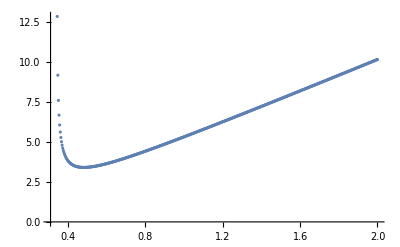

```mathematica
data=Transpose@{frVal,reVal};
ListPlot[data]
```

```mathematica
Export["C:\\Users\\byy\\Desktop\\frVal.txt",frVal,"Table"]
```

C:\Users\byy\Desktop\frVal.txt